```mathematica
V4[r,Ff,Fg]
```

-4.2041564461612558246929913843914011337349321025869 ⅇ^(-1.8897956763949163901043021378977802804729637344946 r)-1/r

## Definition

```mathematica
δ50V
```

{-0.0010112864184230643500148805306756656692007495975031,-0.0031979538931209815977792456738464217491239704203567,-0.010112357866899140505986915285447471584998824147067,-0.031963530999942135580066285495419263636274009590628,-0.10061840240122352411779974957434610910660152958619,-0.30404523064061299584131420827842479776341551966039,-0.7321881886441398085256379622073714870909292729968,1.5706992101715791374523098598121078917781790729407,0.01655287990685862097529993439524812391184369120353,-0.88676155322699035465597610067948784396837490388424,-0.20316806883625407759244658829433575182079243420634,0.68152055882262457337769553340136258946948049641742,-0.14616851862628250847675251201766201303321356306166,0.55479081458935396539221168434804941081019572710449,-1.0538847911917323343668059082008077617705426516002,1.493960729710249209744116352257949168017977212268,-0.035920647188492847603768899283743717562244932101418,-0.922068755563445059353059350473503793718920670425,-1.2240862385461119346183684028990904677821318549192}

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
a=1;ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V2[r_,Fc_,Fd_]=-α/r+Fc E^(-Fd r)/r;
V3[r_,Fe_,Fh_]=-α/r+Fe(E^(-Fh r^2))/r;
V4[r_,Ff_,Fg_]=-α/r+Ff E^(-Fg r);
V5[r_,Fi_,Fj_]=-α/r+Fi E^(-Fj r^2);
```

```mathematica
{Ff,Fg}={-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50.,1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50.};
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[evShifted[[n]],3],1.01 SetPrecision[evShifted[[n]],3]},opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)]]
```

```mathematica
δexpminus10=δ50e[10^-10,V4[r,Ff,Fg]];
δexpminus5=δ50e[10^-5,V4[r,Ff,Fg]];
δ50V=δ50[V4[r,Ff,Fg]];
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979700136220568923737045153765763046169357856) is less than WorkingPrecision (50.).

End with 0.3597647s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095933881080621951847950360718656142026828058) is less than WorkingPrecision (50.).

End with 0.2534541s

NDSolve::precw: The precision of the differential equation ({{2 (0.001+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974420815225174201553345413564726027527601002) is less than WorkingPrecision (50.).

End with 0.3125018s

{1/1000000,-0.031963530999942135580066285495419263636274009590628}    0.312502

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631708196101944706820810514600259947125) is less than WorkingPrecision (50.).

End with 0.3593776s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898866) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22646) is less than WorkingPrecision (50.).

{1/1000000000,-0.0010112864184230643500148805306756656692007495975031}    0.359378

End with 0.4062530s

End with 0.3906296s

{0.001,-0.7321881886441398085256379622073714870909292729968}    0.406253

{0.01,-0.88676155322699035465597610067948784396837490388424}    0.406253

NDSolve::precw: The precision of the differential equation ({{2 (0.003+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.03+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095933881080621951847950360718656142026828058) is less than WorkingPrecision (50.).

End with 0.3281301s

{1/100000,-0.10061840240122352411779974957434610910660152958619}    0.32813

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979647948935045155032628991570275865509771807) is less than WorkingPrecision (50.).

End with 0.3593780s

{1/100000000,-0.0031979538931209815977792456738464217491239704203567}    0.375006

FindRoot::precw: The precision of the argument function (Tan[δ]==10296.9) is less than WorkingPrecision (50.).

End with 0.4218788s

{0.003,1.5706992101715791374523098598121078917781790729407}    0.421879

NDSolve::precw: The precision of the differential equation ({{2 (0.007+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.20601) is less than WorkingPrecision (50.).

End with 0.5625049s

{0.03,-0.20316806883625407759244658829433575182079243420634}    0.562505

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.3137741414855291701290996588875885404116769049) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.07+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112702576834871036503197245326290954321098893) is less than WorkingPrecision (50.).

End with 0.4062521s

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000,-0.30404523064061299584131420827842479776341551966039}    0.406252

End with 0.3906275s

{1/10000000,-0.010112357866899140505986915285447471584998824147067}    0.390628

NDSolve::precw: The precision of the differential equation ({{2 (0.3+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0165544) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.4062541s

{0.007,0.01655287990685862097529993439524812391184369120353}    0.406254

FindRoot::precw: The precision of the argument function (Tan[δ]==0.811179) is less than WorkingPrecision (50.).

End with 0.5622011s

{0.07,0.68152055882262457337769553340136258946948049641742}    0.568205

NDSolve::precw: The precision of the differential equation ({{2 (0.1+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.619716) is less than WorkingPrecision (50.).

End with 0.8196428s

{0.3,0.55479081458935396539221168434804941081019572710449}    0.8196428

NDSolve::precw: The precision of the differential equation ({{2 (0.7+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.147218) is less than WorkingPrecision (50.).

End with 0.5785769s

{0.1,-0.14616851862628250847675251201766201303321356306166}    0.578577

FindRoot::precw: The precision of the argument function (Tan[δ]==12.9891789731678850814023216327706641141661936) is less than WorkingPrecision (50.).

End with 1.0812557s

{1,1.493960729710249209744116352257949168017977212268}    1.09689

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.75911) is less than WorkingPrecision (50.).

End with 0.9062575s

{0.7,-1.0538847911917323343668059082008077617705426516002}    0.9218825

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.03593610455162919837654294256946783416409952901) is less than WorkingPrecision (50.).

End with 1.7187527s

{3,-0.035920647188492847603768899283743717562244932101418}    1.734379

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.3189157216471386286670039213653631845061256852) is less than WorkingPrecision (50.).

End with 2.8378658s

{7,-0.922068755563445059353059350473503793718920670425}    2.884728

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.767747195216944774159169303847381220238135991) is less than WorkingPrecision (50.).

End with 2.6404980s

{10,-1.2240862385461119346183684028990904677821318549192}    2.671733

## FindFit For Lepage’s Data

```mathematica
enDetermineFfg[Ff_?NumberQ,Fg_?Positive,enF_]:=EigenEnergySolo[V4[r,Ff,Fg],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[enF],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->300}];
EvaluateV4[Ff_,Fg_]:=((enDetermineFfg[Ff,Fg,#]-#)&/@{-0.00129205010,-0.00534541931});
FindRoot[(enDetermineFfg[Ff,Fg,#]==#)&/@{-0.00129205010,-0.00534541931},{{Ff,-4.5665},{Fg,2.1}},MaxIterations->200,PrecisionGoal->15,WorkingPrecision->50,StepMonitor:>Print[{{Ff,Fg},EvaluateV4[Ff,Fg]}]]
```

FindRoot::precw: The precision of the argument function ({enDetermineFfg[Ff,Fg,-0.00129205]==-0.00129205,enDetermineFfg[Ff,Fg,-0.00534542]==-0.00534542}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.5665 Power[«2»]-Power[«2»]) u[r$87330]-u''[r$87330]/2==e$87329 u[r$87330],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.5665 Power[«2»]-Power[«2»]) u[r$87661]-u''[r$87661]/2==e$87660 u[r$87661],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.5665 Power[«2»]-Power[«2»]) u[r$87978]-u''[r$87978]/2==e$87977 u[r$87978],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{{-3.421,1.62276},{{-7.66549×10^-7},{-6.5734×10^-6}}}

{{-4.00338,1.82907},{{2.4866×10^-8},{1.88863×10^-7}}}

{{-4.19276,1.88669},{{1.05767×10^-8},{8.81045×10^-8}}}

{{-4.20413,1.88979},{{5.52675×10^-11},{4.63386×10^-10}}}

{{-4.20416,1.8898},{{5.99781×10^-16},{3.83634×10^-15}}}

{{-4.204156446173221504697288,1.889795676398548082772996},{{2.1684×10^-19},{-2.60209×10^-18}}}

{{-4.2041564461612734133513686818994350600797847918142,1.8897956763949249560300627879940266047029139140065},{{6.50521×10^-19},{8.67362×10^-19}}}

{{-4.2041564461612558246791568131070556539496179072622,1.889795676394916390104312141444562630318252292904},{{4.33681×10^-19},{0.}}}

{{-4.2041564461612558246796923394681532360127107649283,1.8897956763949163901042907163003828653276595509912},{{0.},{0.}}}

{{-4.2041564461612558246796923368683900125626293093377,1.8897956763949163901042907145467516527629995188764},{{0.},{0.}}}

{{-4.2041564461612558246796892092810807396928372862605,1.8897956763949163901042885318886493879659296061953},{{0.},{0.}}}

{{-4.2041564461612558246929913819627010995181354672341,1.8897956763949163901043021380218981178881682333878},{{0.},{0.}}}

{{-4.2041564461612558246929913843899274184438638634822,1.8897956763949163901043021378973462880873344499527},{{0.},{0.}}}

{{-4.204156446161255824692991384391401133734932102586,1.8897956763949163901043021378977802804729637344944},{{0.},{0.}}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

{Ff→-4.2041564461612558246929913843914011337349321025869,Fg→1.8897956763949163901043021378977802804729637344946}

```mathematica
{Ff,Fg}={Ff,Fg}/.%38
```

{-4.2041564461612558246929913843914011337349321025869,1.8897956763949163901043021378977802804729637344946}

```mathematica
{Ff,Fg}=First@{{-4.20415644616125582467969233946815323601271076492826667978476766133869477047311`50.,1.88979567639491639010429071630038286532765955099118495220415990555489242190358`50.},{{0.},{0.}}}
```

```mathematica
-1.315132111438484852072861031047068536281585693359375`50. ⅇ^(-0.86249352035843696029360216925852000713348388671875`50. r)-1/r
```

```mathematica
enV4=EigenEnergy[V4[r,Ff,Fg],αSch,{1.*10^-15,2000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.3822,-0.182736,-0.0703652,-0.0371487,-0.0229267,-0.0155492,-0.0112354,-0.00849649,-0.00664955,-0.00534542,-0.00439048,-0.00367033,-0.00311387,-0.00267499,-0.00232276,-0.00203579,-0.00179889,-0.00160106,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$268874]-u''[r$268874]/2==e$268873 u[r$268874],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.38219883569252214593435969435,-0.182735548644295254658587750087,-0.0703651929305044812537815304851,-0.0371486908262773608233301185477,-0.0229266892452571105551498542094,-0.0155492318552683084761160772393,-0.0112354034510922544116147769728,-0.00849649089104768827256034688038,-0.00664954945575757018944033539245,-0.00534541931000000018728048194254,-0.00439047850565455961112147118865,-0.00367033275768893297363647228711,-0.00311386894651937044550988607929,-0.00267499298242404437153454541914,-0.00232276446482712140332469741659,-0.00203578876875439264420689053927,-0.00179888914720533097470179223071,-0.00160105779040614129144723532915,-0.00143415343774481313926261688988,-0.0012920500999999989967522447681}

```mathematica
EigenEnergySolo[V4[r,Ff,Fg],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.03714968384569772],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_enV4.mx",enV4]
```

{{-1.38219883569252214593435969435,-0.182735548644295254658587750087,-0.0703651929305044812537815304851,-0.0371486908262773608233301185477,-0.0229266892452571105551498542094,-0.0155492318552683084761160772393,-0.0112354034510922544116147769728,-0.00849649089104768827256034688038,-0.00664954945575757018944033539245,-0.00534541931000000018728048194254,-0.00439047850565455961112147118865,-0.00367033275768893297363647228711,-0.00311386894651937044550988607929,-0.00267499298242404437153454541914,-0.00232276446482712140332469741659,-0.00203578876875439264420689053927,-0.00179888914720533097470179223071,-0.00160105779040614129144723532915,-0.00143415343774481313926261688988,-0.0012920500999999989967522447681}}

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_enV4.mx"]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end_},opt___]:=Module[{aaa,findroot},aaa=a;
Print["a=",aaa];
findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>Print[{c1,evnhhhc1[c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50]
```

a=1

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000752439232570637242694928969350447881242404080392) is less than WorkingPrecision (50.).

End with 0.8975576s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

End with 0.7122173s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.7343996s

End with 0.7343725s

End with 0.6604398s

End with 0.6885327s

End with 0.6820313s

{-21.,-0.00034627799}

End with 0.6898978s

End with 1.0626452s

End with 0.6769298s

End with 0.8859514s

End with 0.9911252s

{-41.045998916466048986285739947608781382719930015167,-0.00013552032}

End with 0.9653826s

End with 0.8144269s

End with 0.7922926s

End with 0.7984825s

{-42.645306255242529144959815719996656796403051525383,-0.000053950039}

End with 0.7976047s

End with 0.8755074s

End with 0.8595729s

{-43.703077455065765476020374372489935942409722365833,0.000035144668}

End with 0.8631142s

End with 0.8462952s

End with 0.8657812s

{-43.28582463519657051826747048698964541478894715702,-5.030088×10^-6}

End with 0.8967525s

End with 0.8666548s

End with 0.8639994s

{-43.338066854404036576899000059665061724309317420067,-4.1563023×10^-7}

End with 0.8604695s

End with 0.7161520s

End with 0.7152778s

{-43.342772379225281202352914065413086855469356504696,5.3600235×10^-9}

End with 0.7161630s

End with 0.7356390s

End with 0.7356386s

{-43.342712468756062424530900485606875959029642953854,-5.6394249×10^-12}

End with 0.7356997s

End with 0.7266316s

End with 0.7266197s

{-43.342712531723228870288950712286649822374499741607,-7.6438078×10^-17}

End with 0.7344574s

End with 0.7383466s

End with 0.7565425s

{-43.342712531724082353488940994311556953371018724017,1.0902168×10^-24}

End with 0.7448981s

End with 0.7563942s

End with 0.8590342s

{-43.34271253172408235347676798177363023401958689086,-2.1072838×10^-37}

-43.34271253172408235347676798177363023401958689086

-43.34271253172408235347676798177363023401958689086

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_c1.mx",c1];
```

```mathematica
energyVs1=Range@20
```

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.42251,-0.183239,-0.0704381,-0.0371645,-0.0229316,-0.0155511,-0.0112362,-0.00849691,-0.00664978,-0.00534555,-0.00439056,-0.00367038,-0.0031139,-0.00267502,-0.00232278,-0.0020358,-0.0017989,-0.00160106,-0.00143416,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.7519864098917525944450578695217378787953526304973 Power[«2»]-Power[«2»] Erf[«1»]) u[r$13445]-u''[r$13445]/2==e$13444 u[r$13445],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.42251048393239936900846855867,-0.183238867889072899325593331361,-0.0704380940711213211591652750741,-0.0371645388672633116114394714209,-0.0229315562237762254628602890725,-0.0155510989967794797854616505931,-0.0112362380778956671118070217709,-0.00849690782107124512937718542627,-0.00664977604603515837640557530912,-0.00534555087013955862848845336139,-0.00439055906429928322934712787654,-0.00367038429173151124285096852529,-0.0031139031417427358025148337811,-0.0026750163882297983702265056077,-0.00232278091885705229091867706944,-0.00203580060702947894767924335524,-0.00179889783941919638694243040146,-0.0016010642883023065004846473006,-0.00143415837355966632109855621563,-0.00129205390334495505498852367419}

```mathematica
Module[{eeee,timea,timeb},
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-15,3000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-1.4225215],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
timeb=SessionTime[];
Print[{eeee},"    end with ",timeb-timea,"s"];
eeee
]
```

```mathematica
energyVs1[[1]]=First@%
```

```mathematica
energyVs1
```

```mathematica
Abs@((enV4-energyVs1)/enV4)
```

{0.02916486919168898393376631281,0.00275435868122946958881666662,0.0010360398029298381790849866,0.00042661102271578777506313187,0.00021228440212412043577446219,0.0001200793408028509354701829,0.00007428543238752691172837329,0.00004907084923684839772346569,0.0000340760346390072795124536,0.00002461175296619362931925314,0.0000183484885804282160144219,0.0000140407003888983118228415,0.0000109815871999301197023686,8.74985688104073104370127×10^-6,7.08381335260018871141123×10^-6,5.81508026176349283103467×10^-6,4.83198971927539428273781×10^-6,4.05850195048906522509641×10^-6,3.44162257906192935620844×10^-6,2.94365129963477362999906×10^-6}

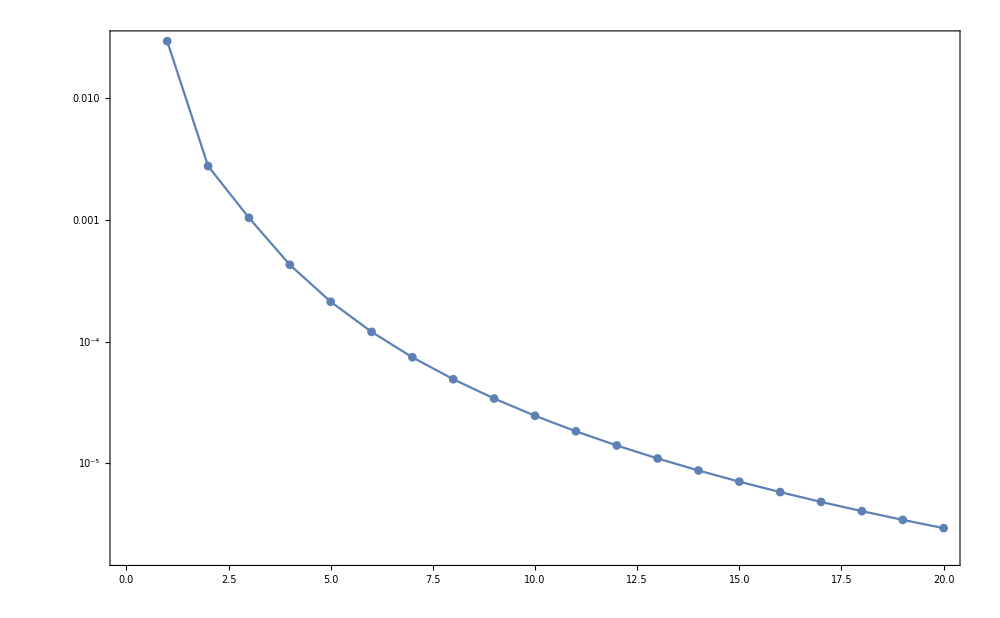

```mathematica
ListLogPlot[Abs@((enV4-energyVs1)/enV4),Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs1.mx",energyVs1];
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs1.mx"];
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
Abs@(δ50V-δVs1)
```

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867636069381632863049406394742931954279706) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.899448) is less than WorkingPrecision (50.).

End with 1.2968851s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974436157707714660150532263638862154161462001) is less than WorkingPrecision (50.).

End with 1.3281380s

{1/1000000000,-0.0010112864188591824570883264135999767291880142576858}    1.312511

End with 1.3437609s

{0.001,-0.73251024636538605290844326155417788665970485661694}    1.328138

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22752) is less than WorkingPrecision (50.).

{1/1000000,-0.031963546326755093055488004018028490004646171847191}    1.359386

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.5937633s

{0.01,-0.88718542301858095340999016511726998522534379862133}    1.593763

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979648100640938515728337816721434633570820005) is less than WorkingPrecision (50.).

End with 1.1718856s

{1/100000000,-0.0031979539082914157861388037333026343838234809816412}    1.171886

FindRoot::precw: The precision of the argument function (Tan[δ]==2165.49) is less than WorkingPrecision (50.).

End with 1.2812597s

{0.003,1.570334538585278931034989151091132087089877541932}    1.28126

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095982979693301507256202683886419907488188124) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

End with 1.3750130s

{1/100000,-0.10061888843330422218922479780931552303224650060014}    1.390639

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.208106) is less than WorkingPrecision (50.).

End with 1.5468896s

{0.03,-0.20517738295883167412974954942342206143526342714492}    1.562515

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0101127030609902778908355197614364206294763073) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.2968872s

{1/10000000,-0.010112358351005039419361696187394830435163070576229}    1.296887

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0162092) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31379136442604294651908205042733350513702864046) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.3593876s

End with 1.2968864s

{0.007,0.016207734975617944436742006847990195551443297740877}    1.359388

{1/10000,-0.30406090981557931925670902101425108152647272227122}    1.296886

FindRoot::precw: The precision of the argument function (Tan[δ]==0.802736) is less than WorkingPrecision (50.).

End with 1.8125170s

{0.07,0.67640677645486765672006048756289629130066546695822}    1.812517

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.582456) is less than WorkingPrecision (50.).

End with 1.9062677s

{0.3,0.52741926274367027921712917555829584996592369211022}    1.921895

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.7519864098917525944450578695217378787953526304973 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.154708) is less than WorkingPrecision (50.).

End with 1.8593927s

{0.1,-0.15349082579501963840554925209251985285329347371867}    1.875019

FindRoot::precw: The precision of the argument function (Tan[δ]==6.1806506247222623897131955352492743906982685417) is less than WorkingPrecision (50.).

End with 3.5000330s

{1,1.4103911040169719673968025492035746929695509184872}    3.515658

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.05111) is less than WorkingPrecision (50.).

End with 2.6718997s

{0.7,-1.117165576051394914976225101793439174284469673787}    2.687524

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.0129176484871277116333998641065559608248591198) is less than WorkingPrecision (50.).

End with 8.9844620s

{7,-1.1097189612021025338588654784662192245571792807058}    9.0313345

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.19276333994309572522255600173839454717429385719) is less than WorkingPrecision (50.).

End with 5.7969301s

{3,-0.1904276484843999699495848256771838122357882487761}    5.82818

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.457692386370330621398573132654253990123780927) is less than WorkingPrecision (50.).

End with 11.4532357s

{10,-1.417162528371515382812653717687838204348096373861}    11.484483

{-0.0010112864188591824570883264135999767291880142576858,-0.0031979539082914157861388037333026343838234809816412,-0.010112358351005039419361696187394830435163070576229,-0.031963546326755093055488004018028490004646171847191,-0.10061888843330422218922479780931552303224650060014,-0.30406090981557931925670902101425108152647272227122,-0.73251024636538605290844326155417788665970485661694,1.570334538585278931034989151091132087089877541932,0.016207734975617944436742006847990195551443297740877,-0.88718542301858095340999016511726998522534379862133,-0.20517738295883167412974954942342206143526342714492,0.67640677645486765672006048756289629130066546695822,-0.15349082579501963840554925209251985285329347371867,0.52741926274367027921712917555829584996592369211022,-1.117165576051394914976225101793439174284469673787,1.4103911040169719673968025492035746929695509184872,-0.1904276484843999699495848256771838122357882487761,-1.1097189612021025338588654784662192245571792807058,-1.417162528371515382812653717687838204348096373861}

{4.361181070734458829243110599872646601827×10^-13,1.5170434188359558059456212634699510561285×10^-11,4.84105898913374780901947358850164246429162×10^-10,1.532681295747542171852260922636837216225656×10^-8,4.8603208069807142504823496941392564497101396×10^-7,0.0000156791749663234153948127358262837630572026108,0.0003220577212462443828052993468063995687755836201,0.000364671586300206417320708720975804688301531008,0.000345144931240676538557927547257928360400393462653,0.0004238697915905987540140644377821412569688947371,0.0020093141225775965373029611290863096144709929386,0.0051137823677569166576350458384662981688150294592,0.00732230716873712992879674007485783982007991065701,0.0273715518456836861750825087897535608442720349943,0.0632807848596625806094191935926314125139270221868,0.083569625693277242347313803054374475048426293781,0.1545070012959071223458159263934400946735433166747,0.187650205638657474505806127992715430838258610281,0.193076289825403448194285314788747736565964518942}

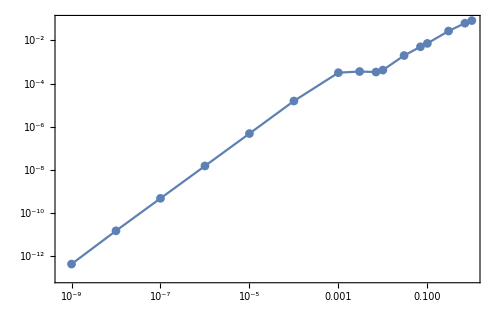

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs1)}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->500]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
δexpminus9=δ50e[ee[[2]],V4[r,Ff,Fg]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631708196101944706820810514600259947125) is less than WorkingPrecision (50.).

End with 0.3027172s

-0.0010112864184230643500148805306756656692007495975031

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->200,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

End with 0.9062505s

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

End with 0.8906354s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9531408s

End with 0.8437589s

End with 0.8437593s

End with 0.8593885s

End with 0.7968879s

End with 0.7812579s

End with 0.9062649s

End with 0.9687597s

End with 0.6875084s

End with 0.8281347s

End with 0.6875105s

End with 0.7968739s

{-36.2846073485848683455598356806,5.8412550011407563669641760073,0.000048354152,0.00015290929}

End with 0.7187705s

End with 0.7812460s

End with 0.7500090s

End with 0.7968982s

End with 0.7343848s

End with 0.7968735s

End with 0.8750230s

End with 1.0156210s

End with 1.0937642s

End with 1.0625134s

{-35.9154194490397907307718548026,5.78600358078768153868615504162,4.8342618×10^-6,0.000015287283}

End with 1.1406398s

End with 1.0468891s

End with 1.0468883s

End with 0.9375125s

End with 1.0156386s

End with 1.0000140s

End with 0.9218858s

End with 1.0625154s

End with 0.8125232s

End with 1.1406422s

End with 0.8281220s

End with 1.0312616s

{-36.3056922742570075203196473575,5.45531818058589715190060363081,4.1917196×10^-6,0.000013255385}

End with 0.8750103s

End with 1.0468887s

End with 0.9218859s

End with 1.0781400s

End with 0.9843880s

End with 1.0625134s

End with 1.0468887s

End with 1.1250148s

End with 0.9843873s

End with 1.0615531s

{-36.2637536276647644520882824144,5.45133647588196434660588203705,4.4320249×10^-8,1.4015361×10^-7}

End with 0.9375141s

End with 1.0156354s

End with 0.9531371s

End with 0.9687762s

End with 0.9374990s

End with 0.9923363s

End with 1.0022645s

End with 0.9687643s

End with 0.9843996s

End with 0.9531269s

{-36.2721675079924378564009062102,5.44394932728545553594203554005,-7.3516061×10^-11,-2.3184092×10^-10}

End with 0.9687606s

End with 1.0312649s

End with 0.9687622s

End with 0.9531380s

End with 0.9843872s

End with 1.0156497s

End with 1.0156271s

End with 0.8593848s

End with 0.8750128s

End with 0.8750123s

End with 0.8906378s

End with 0.8281334s

End with 1.0420734s

End with 0.9861855s

End with 0.9062620s

End with 0.9218875s

End with 0.9510122s

End with 0.8906369s

End with 1.1250140s

End with 1.0468883s

End with 0.9687634s

End with 0.8437598s

End with 0.8750147s

End with 0.8750251s

End with 1.0312468s

End with 0.9687647s

End with 1.0625154s

End with 1.0625125s

End with 0.8750238s

End with 0.9843872s

End with 1.0625269s

End with 0.9218797s

End with 0.7812554s

End with 0.8437594s

End with 0.9218870s

End with 0.9531376s

End with 0.9062620s

End with 0.9218883s

End with 0.9531359s

End with 0.9375126s

{-36.2721881053246393809424083681,5.44393227054383776791152700615,-7.3516032×10^-11,-2.3184083×10^-10}

End with 0.8593876s

End with 0.9062604s

End with 0.9062632s

End with 0.9375105s

End with 0.8125096s

End with 1.0156378s

End with 0.9843897s

End with 0.9218855s

End with 0.8593877s

End with 0.9531355s

End with 1.1093893s

End with 1.0312776s

End with 0.9062616s

End with 0.8906345s

End with 0.8906398s

End with 0.9218850s

End with 0.9375248s

End with 0.8906378s

End with 0.9531355s

End with 0.9375121s

End with 0.9843881s

End with 0.9375138s

End with 0.9062607s

End with 0.8906358s

End with 0.9844065s

End with 1.0468711s

End with 1.0156505s

End with 1.0156386s

End with 0.8750238s

End with 0.9531248s

End with 0.9531389s

End with 0.9219055s

End with 0.9062423s

End with 0.8281491s

End with 0.9531375s

End with 1.0625138s

End with 1.0781400s

End with 0.9375134s

End with 1.1406382s

End with 1.0135333s

{-36.2722079742857402338550709882,5.44391581697733108258361338319,-7.3515974×10^-11,-2.3184065×10^-10}

End with 1.0312657s

End with 1.0000115s

End with 1.0156394s

End with 1.0312641s

End with 1.0312624s

End with 0.9843889s

End with 1.0937639s

End with 0.9843893s

End with 0.9843881s

End with 0.9843902s

{-36.2721580418010362095104162377,5.44395785823272593002308193293,-1.8214719×10^-13,6.1342207×10^-14}

End with 1.0000098s

End with 0.9843885s

End with 1.0156382s

End with 1.0625138s

End with 1.0000131s

End with 1.0468912s

End with 1.2343893s

End with 1.2343942s

End with 1.0781401s

End with 0.9687630s

End with 1.0156415s

End with 1.0156365s

End with 0.9843885s

End with 1.0156382s

End with 1.0156407s

End with 1.0312735s

End with 1.3125051s

End with 1.2187651s

End with 0.8906378s

End with 0.9218879s

End with 0.9843877s

End with 0.9531408s

End with 0.9062715s

End with 1.0312550s

End with 1.0312641s

End with 1.0156349s

End with 1.0000143s

End with 1.0781405s

End with 1.1406402s

End with 1.1093893s

End with 1.0000132s

End with 1.0156501s

End with 1.0468891s

End with 0.9531372s

End with 1.0156402s

End with 0.9531380s

End with 0.9843983s

End with 1.0156386s

{-36.2721977586538120609820445116,5.44392496851604171273306195049,-1.8370578×10^-13,5.6405731×10^-14}

End with 1.0937540s

End with 1.0312768s

End with 1.0156497s

End with 0.9843885s

End with 0.9843885s

End with 1.0625133s

End with 0.9687618s

End with 0.8437606s

End with 0.8906357s

End with 0.9062744s

End with 0.7968850s

End with 0.9375133s

End with 0.8593873s

End with 0.9375104s

End with 0.9062616s

End with 0.7968994s

End with 0.8281343s

End with 0.8906353s

End with 0.9687623s

End with 0.8750300s

End with 1.0156193s

End with 1.0000143s

End with 1.0781536s

End with 1.0312501s

End with 1.1093897s

End with 1.0781392s

End with 1.0781429s

End with 1.0468842s

End with 1.1718903s

End with 1.2187668s

End with 1.2187655s

End with 1.1406395s

End with 1.1250148s

End with 1.0781400s

End with 1.1406414s

End with 1.1875146s

End with 1.2500164s

End with 1.2656419s

End with 1.2343950s

End with 1.1718863s

End with 1.1718907s

End with 1.0781384s

End with 1.1250160s

End with 1.1562772s

End with 1.1406407s

End with 1.0937639s

End with 1.0937655s

End with 1.1250180s

End with 1.1562608s

End with 1.1250156s

End with 1.1562702s

End with 1.0781384s

End with 1.1562657s

End with 1.0937663s

End with 1.1250164s

End with 1.0937647s

End with 1.1093905s

End with 1.1406399s

End with 1.1406407s

End with 1.1875150s

End with 1.1406410s

End with 1.1562764s

{-36.2721977586520138027564697499,5.44392496851753085717776775558,-1.8370578×10^-13,5.6405731×10^-14}

End with 0.9843754s

End with 0.9843894s

End with 1.0312632s

End with 1.0156386s

End with 1.0937684s

End with 1.0000226s

End with 0.9375129s

End with 0.9687618s

End with 0.9062628s

End with 0.9531228s

End with 0.9687663s

End with 1.0312781s

End with 0.9218710s

End with 1.0625125s

End with 0.8906497s

End with 0.9843741s

End with 1.0625142s

End with 0.9843897s

End with 1.0000127s

End with 1.0468887s

End with 1.0312624s

End with 1.0937638s

End with 1.0468904s

End with 1.0312644s

End with 0.9687610s

End with 1.0000251s

End with 0.9844020s

End with 0.9375113s

End with 1.0156501s

End with 1.0156263s

End with 0.9843995s

End with 1.0312522s

End with 1.0312756s

End with 1.0312681s

End with 0.9687462s

End with 0.9687618s

End with 1.0156378s

End with 1.0000128s

End with 1.0312751s

End with 1.0624970s

End with 1.0625158s

End with 0.9531363s

End with 0.9687630s

End with 1.0000254s

End with 0.9843745s

End with 1.0000123s

End with 1.3593790s

End with 1.4843950s

End with 1.4687684s

End with 1.4375187s

End with 1.4375183s

End with 1.2500164s

End with 1.3281421s

End with 1.2656410s

End with 1.2500160s

End with 1.2343918s

End with 1.2031404s

End with 1.2812665s

End with 1.2968916s

End with 1.2343922s

End with 1.2656414s

End with 1.3281417s

End with 1.2343922s

End with 1.2187651s

End with 1.2812673s

End with 1.2812674s

End with 1.2187651s

End with 1.2656427s

End with 1.2656394s

End with 1.1875150s

End with 1.1406394s

End with 1.1875158s

End with 1.1562653s

End with 1.1406403s

End with 1.0937638s

End with 1.1718908s

End with 1.2187651s

End with 1.1718899s

{-36.272197758652021581023366364,5.44392496851752441595698657684,-1.8370578×10^-13,5.6405731×10^-14}

End with 1.1562670s

End with 1.1406386s

End with 1.2187655s

End with 1.1093894s

End with 1.1718900s

End with 1.2500164s

End with 1.1562677s

End with 1.0781372s

End with 0.9843877s

End with 0.9687638s

End with 1.0156377s

End with 1.0937659s

End with 1.1562649s

End with 1.1406394s

End with 1.1250136s

End with 1.0156373s

End with 1.0156402s

End with 1.1406402s

End with 1.1562649s

End with 1.2031413s

End with 1.2919026s

End with 1.1627187s

End with 1.1053877s

End with 1.1250156s

End with 1.0781388s

End with 1.1222739s

End with 1.2656411s

End with 1.2812669s

End with 1.2343930s

End with 1.2656398s

End with 1.1841739s

End with 1.1963706s

End with 1.2031999s

End with 1.0625167s

End with 1.1875141s

End with 1.1701854s

End with 1.2050039s

End with 1.1217398s

End with 1.1475662s

End with 1.1093889s

End with 1.2341064s

End with 1.1562649s

End with 1.2102569s

End with 1.0954352s

End with 1.1250156s

End with 1.1660984s

End with 1.2031408s

End with 1.2031413s

End with 1.2517698s

End with 1.1562620s

End with 1.2018148s

End with 1.1303330s

End with 1.1406399s

End with 1.2492048s

End with 1.1406525s

End with 1.1719244s

End with 1.1406403s

End with 1.0937638s

End with 1.2094937s

End with 1.1718903s

End with 1.2959515s

End with 1.1975894s

End with 1.1378732s

End with 1.2129776s

End with 1.1250143s

End with 1.1506350s

End with 1.1713177s

End with 1.1406390s

End with 1.1268245s

End with 1.2343898s

End with 1.0781393s

End with 1.1402465s

End with 1.1873220s

End with 1.2179653s

End with 1.1842093s

End with 1.1875150s

End with 1.2335268s

End with 1.1562649s

End with 1.2031872s

End with 1.1651853s

End with 1.2043635s

End with 1.1940225s

End with 1.1093894s

End with 1.2180976s

End with 1.1093914s

End with 1.1250135s

End with 1.1967413s

End with 1.2031401s

End with 1.2161794s

End with 1.1518929s

End with 1.1815075s

End with 1.1528450s

End with 1.1878656s

End with 1.2158128s

End with 1.1676350s

End with 1.1096677s

End with 1.2487359s

End with 1.1628846s

End with 1.2073408s

End with 1.2187663s

End with 1.1701784s

End with 1.1718895s

End with 1.2321871s

End with 1.1529374s

End with 1.1406407s

End with 1.1421347s

End with 1.1875158s

End with 1.1875158s

End with 1.1078522s

End with 1.1562657s

End with 1.2144679s

End with 1.2590665s

End with 1.4067904s

End with 1.4610262s

End with 1.3092499s

End with 1.2680559s

End with 1.2656415s

End with 1.1710007s

End with 1.1562649s

End with 1.2187659s

End with 1.1397699s

End with 1.1562673s

End with 1.2025082s

End with 1.0991601s

End with 1.1093893s

End with 1.2017052s

End with 1.2031408s

End with 1.2335079s

End with 1.1984688s

End with 1.1562649s

End with 1.2188890s

End with 1.1094017s

End with 1.2103135s

End with 1.1942767s

End with 1.1530478s

End with 1.1671883s

End with 1.2031425s

End with 1.2425773s

End with 1.1343030s

End with 1.2031413s

End with 1.1969047s

End with 1.2344020s

End with 1.2097675s

End with 1.2690190s

End with 1.2656419s

End with 1.1965593s

End with 1.1406386s

End with 1.2167937s

End with 1.2714351s

End with 1.3764086s

End with 1.3117005s

End with 1.2656415s

End with 1.2657466s

End with 1.1250160s

End with 1.2399165s

End with 1.2692165s

End with 1.2498617s

End with 1.2963845s

End with 1.2656418s

End with 1.1984303s

End with 1.2343909s

End with 1.1576361s

End with 1.2340938s

End with 1.1562653s

End with 1.2183734s

End with 1.1875158s

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-36.2721977586520215810233663642,5.44392496851752441595698657669}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_c2d1.mx",{c2,d1}];
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.59768,-0.180602,-0.0702185,-0.0371215,-0.0229188,-0.0155463,-0.0112341,-0.00849586,-0.00664921,-0.00534522,-0.00439036,-0.00367026,-0.00311382,-0.00267496,-0.00232274,-0.00203577,-0.00179888,-0.00160105,-0.00143415,-0.00129203}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$30443]-u''[r$30443]/2==e$30442 u[r$30443],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.59768493239021475624777002261,-0.180602285051877852618818085847,-0.0702185117971134206293146103933,-0.0371214599143008332974470051318,-0.0229188406610151043940574728745,-0.0155463160955231905914637969381,-0.0112341240725214590654471586895,-0.00849585923549535096319748122829,-0.00664920885965451537642052405268,-0.00534522265055337268275273491084,-0.00439035857161624158403364697779,-0.00367025626873854644588967546166,-0.00311381831204068519843021862491,-0.00267495838866846883434571794221,-0.00232274018200219398474950526731,-0.00203577131904286156605018389185,-0.00179887634763984508391202255213,-0.00160104823004255433088749427384,-0.00143414618079445476762612199714,-0.00129204451143613213420776429603}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs2.mx",energyVs2];
```

```mathematica
EigenEnergySolo[Vs2[r,a ,{c2,d1}],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.02306137918729334],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

```mathematica
energyVs2[[5]]=First@%80
```

```mathematica
energyVs2
```

```mathematica
Abs@((energyVs2-enV4)/enV4)
```

{0.1559009392376804870620149369,0.011674048143582157414734568,0.00208456947650138416587469399,0.0007330248084345833393252564,0.00034233395664094034867888473,0.0001875179283618426694735971,0.0001138702830178270855632014,0.00007434310945979499060452176,0.00005122092937588499680400385,0.00003679027504158593703604727,0.00002731684898663376596452689,0.00002083978631809119394205222,0.0000162609536736751351106933,0.0000129322790014158357540738,0.000010454277777676393057618,8.57147450604850738093744×10^-6,7.11526082959341258857496×10^-6,5.97127951548543201994204×10^-6,5.0600934093796077118704×10^-6,4.3253461045067438328172×10^-6}

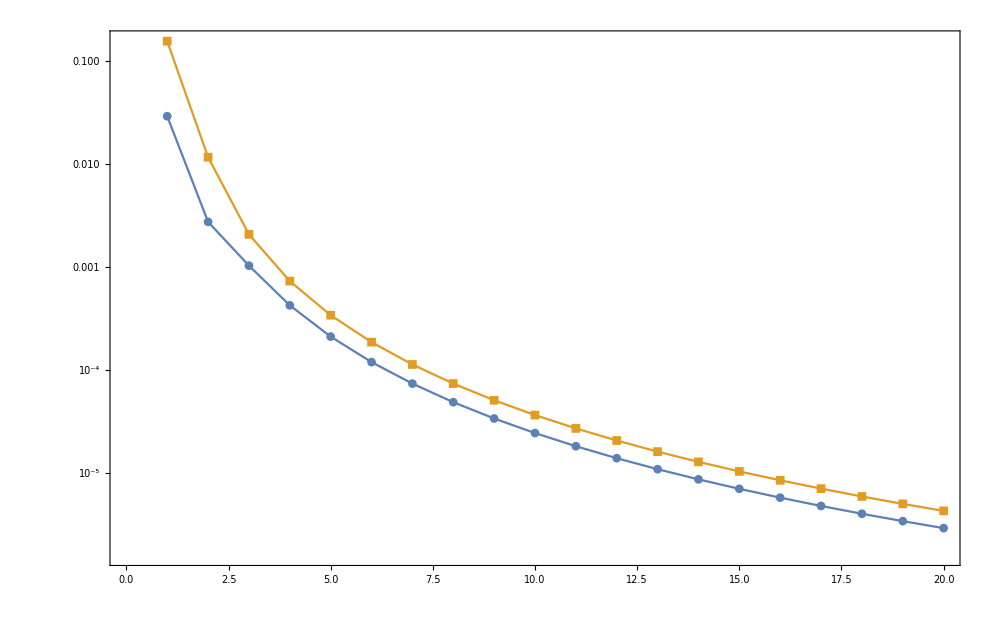

```mathematica
ListLogPlot[{Abs@((energyVs1-enV4)/enV4),Abs@((energyVs2-enV4)/enV4)},Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
Abs@If[#>π/2,#-π,#]&/@(δ50V-δVs2)
```

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898019) is less than WorkingPrecision (50.).

End with 1.6093908s

{0.001,-0.73171949882400191363561046602760688683890210714444}    1.609391

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974398412485998435275260963980173768282491077) is less than WorkingPrecision (50.).

End with 1.8125174s

{1/1000000,-0.031963508620083296530135474525851727925814265338038}    1.812517

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631144138211871644477582276278507432513) is less than WorkingPrecision (50.).

End with 2.1718971s

{1/1000000000,-0.0010112864183666586186937674598539253292889083133489}    2.171897

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22497) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 2.2812717s

{0.01,-0.88616764549789174578702993302899567353252855587269}    2.296897

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2332.18) is less than WorkingPrecision (50.).

End with 1.8593939s

{0.003,-1.570367544076560776765295530438086104047664927035}    1.875017

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095862137570167020409363558913987055271181562) is less than WorkingPrecision (50.).

End with 2.2187708s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979647745605810273078820088262014715904360567) is less than WorkingPrecision (50.).

{1/100000,-0.10061769220494767836336906827967843579017430694924}    2.218771

End with 1.9062669s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000000,-0.0031979538727882660518339748219627132449046575015908}    1.906267

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.203309) is less than WorkingPrecision (50.).

End with 2.7969018s

{0.03,-0.20057521567822032613495324685147294774104347792122}    2.812526

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.017044) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.9531435s

{0.007,0.01704237347547084145765800737931682956316388382671}    1.953144

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31374898115008827846019937806109867905783561609) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.6250162s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112701875109797058392055880714322446486249797) is less than WorkingPrecision (50.).

{1/10000,-0.30402232525594151436786857338658776419601279979157}    1.625016

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.6875162s

NDSolve::precw: The precision of the differential equation ({{2 (1+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000,-0.010112357165245822329764103460288858611027001020669}    1.687516

NDSolve::precw: The precision of the differential equation ({{2 (7+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.820612) is less than WorkingPrecision (50.).

End with 1.7187670s

{0.07,0.68718349419929765226295397660803944088850894733549}    1.718767

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.638186) is less than WorkingPrecision (50.).

End with 2.2968966s

{0.3,0.56802502865766130144522883586720925235108331346384}    2.312523

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.139822) is less than WorkingPrecision (50.).

End with 2.1093946s

{0.1,-0.13892167912000666335960268706071047195210521265138}    2.125019

FindRoot::precw: The precision of the argument function (Tan[δ]==11.15412828341581500790340984499795479709761512) is less than WorkingPrecision (50.).

End with 4.4375417s

{1,1.481382469679319706042011108849408501597711481695}    4.453167

NDSolve::precw: The precision of the differential equation ({{2 (3+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.75243) is less than WorkingPrecision (50.).

End with 4.1562877s

{0.7,-1.0522474172387811184296765729835307326146875029303}    4.156288

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.1180428889949338654401826248631971049969411903) is less than WorkingPrecision (50.).

End with 8.5938315s

{3,-0.11749915296112904909234999526951662711466905163301}    8.6407065

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.7349491831815237357917647171538941278212000642) is less than WorkingPrecision (50.).

End with 13.7657544s

{7,-1.0479212367237168717692113681282568216875341278212}    13.812631

NDSolve::precw: The precision of the differential equation ({{2 (10+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.709299164586707002391223102401612384687840108) is less than WorkingPrecision (50.).

End with 10.5157250s

{10,-1.361558455600239308579285419002701179847124985905}    10.562601

{-0.0010112864183666586186937674598539253292889083133489,-0.0031979538727882660518339748219627132449046575015908,-0.010112357165245822329764103460288858611027001020669,-0.031963508620083296530135474525851727925814265338038,-0.10061769220494767836336906827967843579017430694924,-0.30402232525594151436786857338658776419601279979157,-0.73171949882400191363561046602760688683890210714444,-1.570367544076560776765295530438086104047664927035,0.01704237347547084145765800737931682956316388382671,-0.88616764549789174578702993302899567353252855587269,-0.20057521567822032613495324685147294774104347792122,0.68718349419929765226295397660803944088850894733549,-0.13892167912000666335960268706071047195210521265138,0.56802502865766130144522883586720925235108331346384,-1.0522474172387811184296765729835307326146875029303,1.481382469679319706042011108849408501597711481695,-0.11749915296112904909234999526951662711466905163301,-1.0479212367237168717692113681282568216875341278212,-1.361558455600239308579285419002701179847124985905}

{5.64057313211130708217403399118412841542×10^-14,2.0332715545945270851883708504219312918766×10^-11,7.01653318176222811825158612973971823126399×10^-10,2.237985883904993081096956753571045974425259×10^-8,7.1019627584575443068129466767331642722263694×10^-7,0.0000229053846714814734456348918370335674027198688,0.0004686898201378948900274961797646002520271658524,0.000525899341653324245037993029308888371325399399,0.00048949356861222048235807298406870565132019262318,0.0005939077290986088689461676504921704358463480115,0.0025928531580337514574933414428628040797489562851,0.0056629353766730788852584432066768514190284509181,0.00724683950627584511714982495695154108110835041028,0.0132342140683073360530171515191598415408875863593,0.00163737395295121593712933521727702915585514867,0.01257826003092950370210524340854066642026573057,0.08157850577263620148858109598577290955242411953159,0.125852481160271812416152017654753027968613457396,0.137472217054127373960917016103610712064993130986}

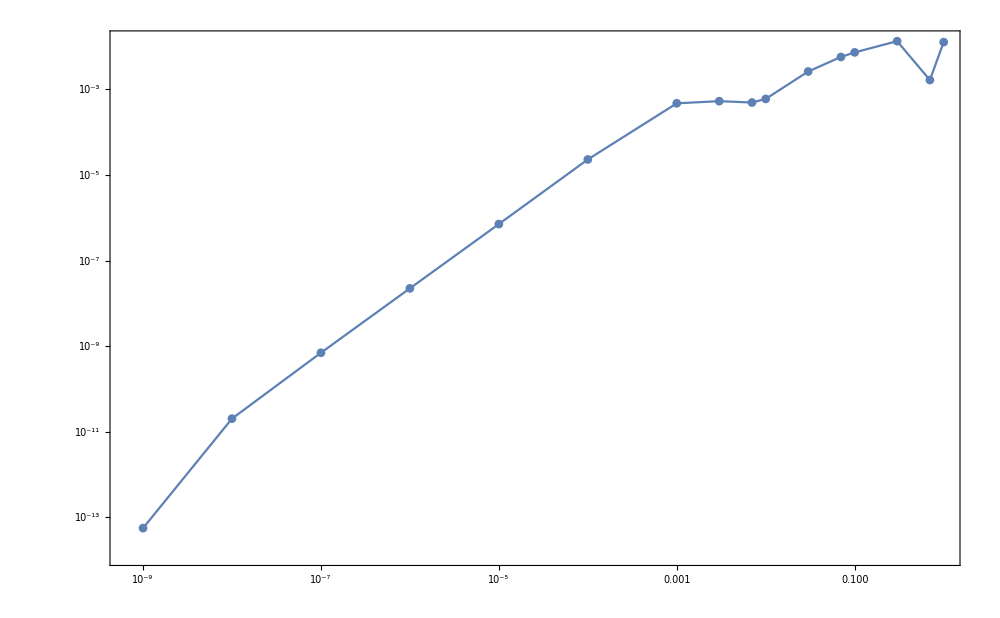

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@If[#>π/2,#-π,#]&/@(δ50V-δVs2)}],Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_c1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_c2d1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_efV4.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_efVs2.mx"]
```

```mathematica
nRange=20;
```

```mathematica
AbsoluteTiming[efV4=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V4[r,Ff,Fg],enV4[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-1.38219883569252214593435969435 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0112354034510922544116147769728 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00534541931000000018728048194254 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0371486908262773608233301185477 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00849649089104768827256034688038 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00439047850565455961112147118865 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.182735548644295254658587750087 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0229266892452571105551498542094 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00664954945575757018944033539245 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00367033275768893297363647228711 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0703651929305044812537815304851 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0155492318552683084761160772393 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00311386894651937044550988607929 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00232276446482712140332469741659 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00179888914720533097470179223071 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00267499298242404437153454541914 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00203578876875439264420689053927 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00160105779040614129144723532915 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00143415343774481313926261688988 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0012920500999999989967522447681 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1328.61,{9.16469666374×10^-1396                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-8.76787738327×10^-472                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],7.259×10^-270                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.20942×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.96817×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.47749×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.29983×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.39821×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.90856×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.088×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79526×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.000015697                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.5726                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.92796×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.13706×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.88859×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186002                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2851.63                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28856×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.38815×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

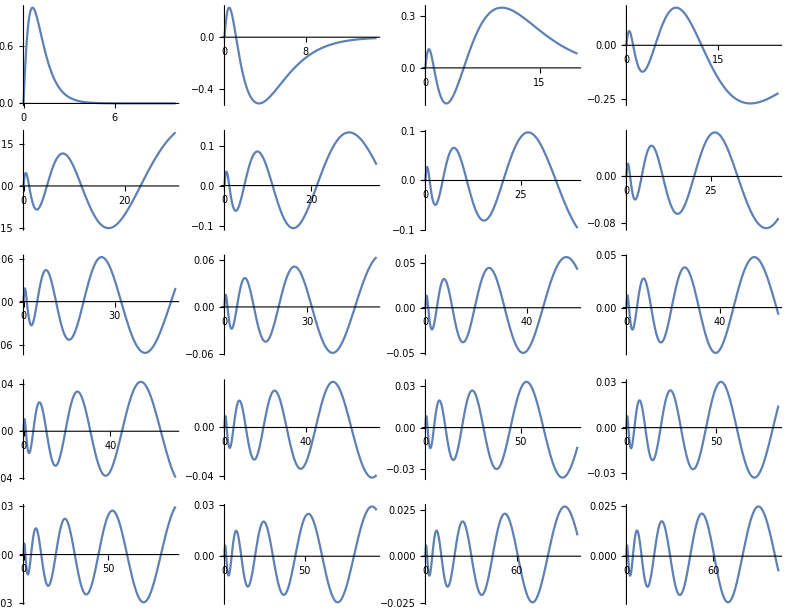

```mathematica
GraphicsGrid@Partition[Table[Plot[efV4[[n]],{r,0,5+5n},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full],{n,1,20}],4]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_efV4.mx",efV4];
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.59768493239021475624777002261 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371214599143008332974470051318 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112341240725214590654471586895 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534522265055337268275273491084 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849585923549535096319748122829 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439035857161624158403364697779 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229188406610151043940574728745 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.180602285051877852618818085847 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664920885965451537642052405268 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367025626873854644588967546166 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155463160955231905914637969381 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0702185117971134206293146103933 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311381831204068519843021862491 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232274018200219398474950526731 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179887634763984508391202255213 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414618079445476762612199714 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267495838866846883434571794221 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577131904286156605018389185 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160104823004255433088749427384 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129204451143613213420776429603 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1531.75,{1.78314592281×10^-1504                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.10407976007×10^-468                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.60229×10^-269                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.48598×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],5.36302×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.53005×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.37919×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.49767×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.92102×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.11388×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.80046×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.000015729                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.7067                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.93269×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.14706×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.89134×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0186141                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2853.31                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.28918×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.39144×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_efVs2.mx",efVs2];
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,If[n>15,4000,b]},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,If[n>15,4000,b]},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
Plot[Evaluate@D[efV4[[1]],{r,2}],{r,0,10^-40},PlotRange->All]
```

```mathematica
NIntegrate[D[efV4[[1]],{r,2}]^2,{r,10^-20,2000}]
```

```mathematica
REAL=Table[NIntegrate[D[efV4[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange}];
N[%,6]
REF=Table[NIntegrate[D[efV4[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange-2,nRange}];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (8.39916649383×10^-2791 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},«46»,{50,49},«57160»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {5.624646708730938607335438917576714372703689761820787172894237025194998365858626757107002511030570386×10^-20}. NIntegrate obtained 28.88557523053066235396668549507332053735032277499420236197102556869231614741049094571100417271994518 and 1.604516181369513226166043919580952174113679269585939772173841057051332529014997219561087906655388361×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.6875673808×10^-943 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«21029»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.951338699079038695980151140466772451665462513299697789330505305028341413657623990150620331846990577 and 3.420638320929013299881732557281455866387675571473030174066068345904721144126133902263787341300846724×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (5.26931378681817×10^-539 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«15225»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.3996282948612724565722942996895067192744546507965830064873085581952605968808456239283609369840169252}. NIntegrate obtained 0.7262694867176725486362963239580698417846620480560149654772806295741337205623377307268035428883830773 and 6.623626845791772729883887014562087765864985444358652425008143231883953646163687689698671533591266727×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.2841973401623147208076140190979006933972171161331111153298419132622882442665804502123018824044230521 and 1.615259641967250074586031556330905733884143745107194839700356316083158126454481178927425523973163154×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {3.61119061244958790171474647910621066056372195000174044421273499762015449596641923592298185068989785×10^-20}. NIntegrate obtained 0.1394467199294625377171114973134044273864197533441860759017852875533530245042263691388066978917785762 and 7.981085194891492269261345137612723374096420495413539384932916510582372550212164052140729287440913069×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.02223346209090080076989625043344914820577652505303281561757892197567820348648410188117790756990595218 and 4.118237510561522562278749817802300636863088109814137674703819218202573292737547460350723502645665796×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{28.8856,2.95134,0.726269,0.284197,0.139447,0.0784988,0.0484813,0.0320124,0.0222335,0.0160645,0.0119822,0.00917383,0.00717879,0.00572273,0.00463526,0.00380676,0.0031645,0.00265897,0.00225562,0.0019299}

NIntegrate::precw: The precision of the argument function (8.1318×10^6 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002658966816430905666884995333681942059549163202674950072217229278986281376013563364052661168869671534 and 8.905642649218314295189676797651420176927230422781917342839041946220816814230867664583035887570990685×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.66039×10^16 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},«43»,{48,47},{49,48},{50,49},«10675»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.4015958180240491137741055404366936476658616793489498425945245598821641241571420955121043288866874×10^-20}. NIntegrate obtained 0.002255624180404716092746995934847501020107021206672294623977087018794716254137949413290218154829291932 and 3.762009534180980640232283081156467155741161699553862472097378701980011716229559230618533877662610664×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.08084×10^-15 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,4000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},«43»,{48,47},{49,48},{50,49},«11413»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001929903102219700673514520999632595155633203012797478436987245441604889690794220442193105970976705162 and 8.440945630149760702913334779505479836824289666909020236900163463059322400389345183363712245867840141×10^-23 for the integral and error estimates.

{0.00265897,0.00225562,0.0019299}

### Matrix element in V_eff^(a^2)

```mathematica
AbsoluteTiming@Module[{n=19},ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium]}}
]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]
Abs@((%-REAL[[20]])/REAL[[20]])
```

```mathematica
AbsoluteTiming[efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
Module[{n=14,efunction},
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]]
]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,If[#>15,4000,2000]},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,If[#>15,4000,2000]][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{(*15,*)20})==(REF[[#]]&/@{(*2,*)3})](*/.Z->1*),{γ,-1,-10},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10,MaxIterations->10000]
((p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{15,20})-(REF[[#]]&/@{2,3}))/(REF[[#]]&/@{2,3})/.RESVs1
```

```mathematica
p4Vs1=p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

```mathematica
ListLogPlot[%161,Joined->True,PlotMarkers->{Automatic}]
```

### Matrix element in V_eff^(a^4)

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs2)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (3.17960938204×10^-3008 (InterpolatingFunction[«1»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8445789641266144944212279940045698592858349664084352631044034669057411727125104306627001254743629111}. NIntegrate obtained 7.143641268598197447374879493722941317815787791940459151613482645175134457750709091711131179483175316 and 9.713499465027468181690375578238809965221696381312719668761691976115191980434249266529686982430153075×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.2189921166×10^-936 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.604494231154101818442778211268971938614290141244898008954531888790584717558475854626065590457665005}. NIntegrate obtained 1.702166795667091139231134292660346122924233796489173551333865518543088024317337804146866502029413022 and 1.993096078139770580008749401823690911662486875832713262444436774624686397267934147894284679089312314×10^-17 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (2.56733291616243×10^-538 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},«45»,{48},{49},«14411»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5270914753719772553401979316420336935041806355009702710391387040978357774950841308273452651322992314}. NIntegrate obtained 0.4533185360972809484286826991593944909852705334990438982309474317982867411853657419137679011847228707 and 2.358890403405793021979657350595512993400656489194464964348752332494323337179472070549154463468710798×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08945665398102921718237732750588101950666368140030360846673306754937122849539308383743624619764162566 and 1.043727434806348971773914849284286957981054143595646276720804983016881858977991345291376870804882645×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.05061337211376130780254086995827775649513802739946392799262801744516482448274295575041317178832081198 and 4.411063493850585838354179156586754036255636718665851529943756628551446820072702667613753876098597249×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.03136384777911224018993165744012348601965973705388272409231720901435707584413235874017773602836318003 and 2.154986564589709334850812315071644463115212398360087974304514685635854038307212019117907353778500191×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{7.14364,1.70217,0.453319,0.180746,0.0894567,0.0506134,0.0313638,0.0207592,0.0144436,0.0104506,0.00780363,0.00598009,0.00468318,0.00373572,0.00302752,0.00248759,0.00206877,0.00173893,0.00147564,0.00126293}

{0.752692,0.423256,0.375826,0.364013,0.358489,0.355234,0.353073,0.351528,0.350366,0.34946,0.348732,0.348135,0.347636,0.347213,0.346849,0.346533,0.346256,0.346011,0.345793,0.345598}

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{18,19,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10]
```

NIntegrate::precw: The precision of the argument function (8.1414×10^6 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},«39»,{45},{46},{47},{48},{49},«10917»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001738933911455073569004175845513524138180994335477147934208969069041699710889599999559144907640414314 and 4.22938708583708243192826089155802377121085602975155229410513684449415006279648420322423442440963927×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (516927. ⅇ^(-r^2/2) («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.6140946128494314403500180951529844574633690172516301826439069198990909550805314328498463920695992131}. NIntegrate obtained 2.331531703780808615581921705288484906048091933780595601365064261403071560782669045887129085957505618×10^-6 and 1.004139105874367673619626569242295651750105785836846115910816981791972112620930697703813981156555055×10^-29 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (8.1414×10^6 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},«39»,{45},{46},{47},{48},{49},«10917»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.614094601638118035095275993523014181510122117959895486666471967319663446385924580059391445452299442}. NIntegrate obtained -2.811968186622011638855083192460302142848516531259527477118547749674292442519570736746703210018684758×10^-6 and 1.428471636186967280886983764476703678664883257118457943714041426182315611038866602398512825777020269×10^-28 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001475644120112911987393825235583793546796583625975042536387459782997218495852397228185193975347470723 and 1.01014166551796643026043529069978589402011111350364368728130058100096228991515527217936776232543994×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001262932296625375710213508180737676412623186830228870506788989328202664602794352956037789237574055748 and 6.94246918911507140263408536147572310712497038881249133049247917770129179177673275317462768363399828×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5907866252600485961439244038992224730010433973811797763512864225777280563515928595866611632821978028}. NIntegrate obtained 1.690078433918328538667269462878419947408261285677262999903277908902479823720410190193349885872511805×10^-6 and 1.490316542994156007547554217829184708091700000377815263532258555142793915782079033251730859720494816×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{Z→1.0024145431110549879902735757407041287262875515584,γ→265.16804387702052531449796531399792999218156272537,η→-105.82853474883086177361597886392255970137042733186}

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (3.17960938204×10^-3008 (InterpolatingFunction[«1»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8445789641266144944212279940045698592858349664084352631044034669057411727125104306627001254743629111}. NIntegrate obtained 7.143641268598197447374879493722941317815787791940459151613482645175134457750709091711131179483175316 and 9.713499465027468181690375578238809965221696381312719668761691976115191980434249266529686982430153075×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (2.01884960516×10^-3009 ⅇ^(-r^2/2) (InterpolatingFunction[«1»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8445793021193089545779598165281917716814905938324922892721177126306578537923262458939516943061138044}. NIntegrate obtained 0.03908260300224699574276613457833946355127022331498023436234540387867651672114662815805262326323790525 and 1.130851671511452613002241737547655974224917781405709129217454106250576331015775536313071204769997494×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.17960938204×10^-3008 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[«1»][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.8445793021193089545779598165281917716814905938324922892721177126306578537923262458939516943061138044}. NIntegrate obtained -0.08595795414643661063490134880908705613640280420503336569639364865585376507854529609753358909997055613 and 2.410394771313255528536424418425072917077729927502031648053676206997686221105197353241194770880427436×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08945665398102921718237732750588101950666368140030360846673306754937122849539308383743624619764162566 and 1.043727434806348971773914849284286957981054143595646276720804983016881858977991345291376870804882645×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.05061337211376130780254086995827775649513802739946392799262801744516482448274295575041317178832081198 and 4.411063493850585838354179156586754036255636718665851529943756628551446820072702667613753876098597249×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.03136384777911224018993165744012348601965973705388272409231720901435707584413235874017773602836318003 and 2.154986564589709334850812315071644463115212398360087974304514685635854038307212019117907353778500191×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{26.6212,2.80983,0.721807,0.283721,0.13936,0.0784772,0.0484748,0.0320102,0.0222326,0.0160642,0.0119821,0.00917377,0.00717876,0.00572271,0.00463525,0.00380676,0.0031645,0.00265897,0.00225562,0.0019299}

{0.0783929,0.0479459,0.00614489,0.00167487,0.000624426,0.000275611,0.000134736,0.000070289,0.0000382041,0.0000212644,0.0000119422,6.67417×10^-6,3.65701×10^-6,1.91929×10^-6,9.32546×10^-7,3.93785×10^-7,1.19107×10^-7,0.,0.,0.}

## ψ_0 in effective theory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
REALψ0=NLimit[efV4[[#]]/(r √(4π)),r->0]&/@Range@nRange
REF=NLimit[efV4[[#]]/(r √(4π)),r->0]&/@{19,20};
```

{1.10034,0.290936,0.140229,0.0866842,0.060325,0.0450743,0.0353219,0.0286423,0.0238319,0.0202321,0.0174556,0.0152607,0.0134902,0.0120374,0.0108279,0.00980818,0.00893905,0.00819111,0.00754195,0.00697422}

```mathematica
FALSEψ0=NLimit[efVs2[[#]]/(√(4π)r),r->0,Scale->10]&/@Range@nRange
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

{0.565701,0.188027,0.0928923,0.0576097,0.0401303,0.029997,0.0235115,0.0190676,0.0158663,0.0134704,0.0116222,0.0101611,0.00898236,0.00801514,0.00720985,0.00653092,0.00595223,0.00545423,0.005022,0.00464398}

{0.565701,0.188027,0.0928923,0.0576097,0.0401303,0.029997,0.0235115,0.0190676,0.0158663,0.0134704,0.0116222,0.0101611,0.00898236,0.00801514,0.00720985,0.00653092,0.00595223,0.00545423,0.005022,0.00464398}

{0.485884,0.353719,0.337566,0.335407,0.334766,0.334499,0.334364,0.334287,0.334239,0.334207,0.334185,0.334169,0.334157,0.334148,0.334141,0.334136,0.334131,0.334127,0.334124,0.334122}

```mathematica
ψ0True[n_,d_][γ_,η_,{optpsi___}]:=√(4π)(γ NIntegrate[efVs2[[n]]/r δa[r] r^2,{r,0,d},optpsi]+η a^2 NIntegrate[efVs2[[n]]/r Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,d},optpsi])
```

```mathematica
RES=FindRoot[Thread[ψ0True[#,2000][γ,η,{MaxRecursion->20}]&/@{19,20}==(REF[[#]]&/@{1,2})],{{γ,0,-2},{η,0,-2}},AccuracyGoal->10,MaxIterations->100000,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ({2 √π (-0.0000467918 γ-0.000581181 η)==0.00754195,2 √π (-0.000043275 γ-0.00053737 η)==0.00697422}) is less than WorkingPrecision (30.).

{γ→-21.5576175700314674336214598554,η→-1.92508917134427697802191092107}

```mathematica
ψ0Vs1=ψ0True[#,If[#>15,4000,2000]][γ,η,{MaxRecursion->20}]&/@Range@nRange/.RES;
N[%,6]
Abs@((REALψ0-ψ0Vs1)/REALψ0);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.13218418041×10^-1505 ⅇ^(-r^2/2) r InterpolatingFunction[«1»][r]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (1.78314592281×10^-1504 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-2.72026,0.278433,0.139408,0.0865434,0.0602878,0.0450617,0.0353169,0.0286401,0.0238309,0.0202316,0.0174553,0.0152606,0.0134901,0.0120374,0.0108279,0.00980817,0.00893905,0.00819111,0.00754195,0.00697422}

{3.4722,0.0429778,0.00585104,0.00162431,0.000616887,0.000278879,0.000140416,0.0000757981,0.0000428178,0.0000248529,0.0000146312,8.59823×10^-6,4.96577×10^-6,2.79119×10^-6,1.46071×10^-6,6.88104×10^-7,2.55631×10^-7,3.88475×10^-8,9.45782×10^-10,9.43085×10^-10}